# Pango analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/pango-countries

## Setup

### Parameters

```mathematica
dataset="pango-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=300;
```

```mathematica
gridCount=1;
```

```mathematica
rtMax=1.6;
```

```mathematica
rtMin=0.6;
```

### Date ticks

```mathematica
dateTicks={"2022-03-01","2022-04-01","2022-05-01","2022-06-01","2022-07-01","2022-08-01","2022-09-01","2022-10-01","2022-11-01","2022-12-01","2023-01-01","2023-02-01"};
```

### Countries

```mathematica
countriesToDrop={};
```

## Variants and colors

### Import

```mathematica
variantData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=variantData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
variantData=Drop[variantData,1];
```

```mathematica
variants=Union[variantData[[All,3]]]
```

{BA.2,BA.5,BA.5.1,BA.5.2,BA.5.2.1,BA.5.2.6,BF.7,BN.1,BN.1.3,BQ.1,BQ.1.1,BQ.1.10,BQ.1.10.1,BQ.1.1.1,BQ.1.11,BQ.1.1.10,BQ.1.1.13,BQ.1.1.18,BQ.1.12,BQ.1.1.3,BQ.1.13,BQ.1.13.1,BQ.1.1.32,BQ.1.1.4,BQ.1.14,BQ.1.1.41,BQ.1.1.5,BQ.1.18,BQ.1.2,BQ.1.22,BQ.1.25.1,BQ.1.28,BQ.1.3,CH.1.1,CK.1,other,XBB,XBB.1,XBB.1.5,XBB.1.5.1,XBB.2}

```mathematica
n=Length[variants]
```

41

### Max frequency

```mathematica
variantFrequencyMapping=Table[variant->Max[Cases[variantData,x_/;x[[3]]==variant][[All,11]]],{variant,variants}];
```

```mathematica
highFrequencyVariants=Cases[variantFrequencyMapping,x_/;x[[2]]>=0.005][[All,1]];
```

```mathematica
Length[highFrequencyVariants]
```

39

```mathematica
lowFrequencyVariants=Complement[variants,highFrequencyVariants];
```

```mathematica
Length[lowFrequencyVariants]
```

2

```mathematica
variants=Join[highFrequencyVariants,lowFrequencyVariants];
```

```mathematica
n=Length[variants]
```

41

### Variant to clade mapping and clade colors

```mathematica
toHexString[n_Integer]:=StringJoin[ToString/@(IntegerDigits[n,16]/.Thread[Range[10,15]->CharacterRange["A","F"]])]
```

```mathematica
rgbColorToHex[rgbColor_]:="#"<>StringJoin[Map[toHexString[Round[#*255]]&,Level[rgbColor,1]]]
```

```mathematica
start[n_]:=0.05;
```

```mathematica
stop[n_]:=0.99;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
startGrays[n_]:=0.35;
```

```mathematica
stopGrays[n_]:=0.65;
```

```mathematica
gapGrays[n_]:=(stopGrays[n]-startGrays[n])/(n-1)
```

```mathematica
makeGrays[n_]:=Table[GrayLevel[i],{i,startGrays[n],stopGrays[n],gapGrays[n]}];
```

```mathematica
variantToClade=Map[#[[1]]->#[[2]]&,Drop[Import["../../data/pango-countries/pango_aliasing.tsv","Table","Numeric"->False],1]];
```

```mathematica
clades={"other","21L","22A","22B","22C","22D","22E","22F","23A"};
```

```mathematica
cladeColors=Prepend[makeColors[Length[clades]-1],Gray]
```

{GrayLevel[0.5],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.24442189714285714, 0.35425512, 0.8136703542857143],RGBColor[0.3112192114285714, 0.5923928742857142, 0.7305370971428573],RGBColor[0.4503775714285713, 0.7087464457142857, 0.5158382742857144],RGBColor[0.6460493028571428, 0.74327364, 0.33515914857142864],RGBColor[0.831986057142857, 0.6938050571428572, 0.24765657142857148],RGBColor[0.9022855371428572, 0.49372713142857155, 0.19958264000000003],RGBColor[0.86067868, 0.15704232000000032, 0.13666448000000006]}

```mathematica
cladeToColor=MapThread[#1->#2&,{clades,cladeColors}]
```

{other→GrayLevel[0.5],21L→RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],22A→RGBColor[0.24442189714285714, 0.35425512, 0.8136703542857143],22B→RGBColor[0.3112192114285714, 0.5923928742857142, 0.7305370971428573],22C→RGBColor[0.4503775714285713, 0.7087464457142857, 0.5158382742857144],22D→RGBColor[0.6460493028571428, 0.74327364, 0.33515914857142864],22E→RGBColor[0.831986057142857, 0.6938050571428572, 0.24765657142857148],22F→RGBColor[0.9022855371428572, 0.49372713142857155, 0.19958264000000003],23A→RGBColor[0.86067868, 0.15704232000000032, 0.13666448000000006]}

### Colors

```mathematica
colorMappingForClade[clade_]:=Module[{pos,shades,tints,col},
pos=Flatten[Position[variants,x_/;(x/.variantToClade)==clade]];
If[Length[pos]>0,
shades=Reverse[Table[Darker[clade/.cladeToColor,x],{x,0,0.5,1/(Length[pos])}]];
tints=Drop[Table[Lighter[clade/.cladeToColor,x],{x,0,0.5,1/(Length[pos])}],1];
col=Join[shades,tints];
Table[variants[[pos[[i]]]]->col[[i]],{i,Length[pos]}],
{}
]
]
```

```mathematica
variantColorMapping=Flatten[Map[colorMappingForClade,clades]]
```

{other→RGBColor[0.5, 0.5, 0.5],BA.2→RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],BA.5→RGBColor[0.1778395493877551, 0.338510213877551, 0.41744976979591847],BA.5.1→RGBColor[0.22229943673469388, 0.42313776734693875, 0.521812212244898],BA.5.2→RGBColor[0.2667593240816326, 0.5077653208163264, 0.6261746546938777],BA.5.2.1→RGBColor[0.3112192114285714, 0.5923928742857142, 0.7305370971428573],BA.5.2.6→RGBColor[0.40961646693877546, 0.6506224636734693, 0.7690317975510206],BF.7→RGBColor[0.5080137224489796, 0.7088520530612245, 0.8075264979591837],CK.1→RGBColor[0.6064109779591836, 0.7670816424489795, 0.846021198367347],BN.1→RGBColor[0.43069953523809523, 0.49551575999999997, 0.22343943238095243],BN.1.3→RGBColor[0.6460493028571428, 0.74327364, 0.33515914857142864],CH.1.1→RGBColor[0.7640328685714285, 0.8288490933333333, 0.5567727657142858],BQ.1→RGBColor[0.4159930285714285, 0.3469025285714286, 0.12382828571428574],BQ.1.1→RGBColor[0.4506591142857142, 0.37581107261904767, 0.13414730952380954],BQ.1.10→RGBColor[0.4853251999999999, 0.4047196166666667, 0.14446633333333336],BQ.1.10.1→RGBColor[0.5199912857142857, 0.4336281607142858, 0.15478535714285718],BQ.1.11→RGBColor[0.5546573714285714, 0.46253670476190484, 0.165104380952381],BQ.1.1.10→RGBColor[0.589323457142857, 0.4914452488095239, 0.1754234047619048],BQ.1.1.13→RGBColor[0.6239895428571427, 0.5203537928571429, 0.1857424285714286],BQ.1.1.18→RGBColor[0.6586556285714285, 0.549262336904762, 0.1960614523809524],BQ.1.12→RGBColor[0.6933217142857142, 0.578170880952381, 0.20638047619047623],BQ.1.1.3→RGBColor[0.7279877999999999, 0.6070794250000001, 0.21669950000000004],BQ.1.13→RGBColor[0.7626538857142856, 0.6359879690476191, 0.22701852380952386],BQ.1.1.32→RGBColor[0.7973199714285713, 0.6648965130952382, 0.23733754761904766],BQ.1.1.4→RGBColor[0.831986057142857, 0.6938050571428572, 0.24765657142857148],BQ.1.14→RGBColor[0.838986638095238, 0.7065631797619049, 0.2790042142857143],BQ.1.1.41→RGBColor[0.845987219047619, 0.7193213023809525, 0.3103518571428572],BQ.1.1.5→RGBColor[0.8529877999999999, 0.7320794250000001, 0.34169950000000004],BQ.1.18→RGBColor[0.8599883809523808, 0.7448375476190476, 0.3730471428571429],BQ.1.2→RGBColor[0.8669889619047618, 0.7575956702380953, 0.4043947857142858],BQ.1.22→RGBColor[0.8739895428571427, 0.7703537928571429, 0.43574242857142864],BQ.1.25.1→RGBColor[0.8809901238095237, 0.7831119154761905, 0.4670900714285715],BQ.1.28→RGBColor[0.8879907047619047, 0.7958700380952382, 0.49843771428571426],BQ.1.3→RGBColor[0.8949912857142857, 0.8086281607142858, 0.5297853571428571],BQ.1.1.1→RGBColor[0.9019918666666666, 0.8213862833333334, 0.5611330000000001],BQ.1.13.1→RGBColor[0.9089924476190475, 0.834144405952381, 0.5924806428571429],XBB→RGBColor[0.6015236914285715, 0.32915142095238104, 0.13305509333333337],XBB.1→RGBColor[0.9022855371428572, 0.49372713142857155, 0.19958264000000003],XBB.2→RGBColor[0.9348570247619048, 0.6624847542857144, 0.4663884266666667],XBB.1.5→RGBColor[0.43033934, 0.07852116000000016, 0.06833224000000003],XBB.1.5.1→RGBColor[0.86067868, 0.15704232000000032, 0.13666448000000006]}

```mathematica
highFrequencyColors=highFrequencyVariants/.variantColorMapping
```

{RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.1778395493877551, 0.338510213877551, 0.41744976979591847],RGBColor[0.22229943673469388, 0.42313776734693875, 0.521812212244898],RGBColor[0.2667593240816326, 0.5077653208163264, 0.6261746546938777],RGBColor[0.3112192114285714, 0.5923928742857142, 0.7305370971428573],RGBColor[0.40961646693877546, 0.6506224636734693, 0.7690317975510206],RGBColor[0.5080137224489796, 0.7088520530612245, 0.8075264979591837],RGBColor[0.43069953523809523, 0.49551575999999997, 0.22343943238095243],RGBColor[0.6460493028571428, 0.74327364, 0.33515914857142864],RGBColor[0.4159930285714285, 0.3469025285714286, 0.12382828571428574],RGBColor[0.4506591142857142, 0.37581107261904767, 0.13414730952380954],RGBColor[0.4853251999999999, 0.4047196166666667, 0.14446633333333336],RGBColor[0.5199912857142857, 0.4336281607142858, 0.15478535714285718],RGBColor[0.5546573714285714, 0.46253670476190484, 0.165104380952381],RGBColor[0.589323457142857, 0.4914452488095239, 0.1754234047619048],RGBColor[0.6239895428571427, 0.5203537928571429, 0.1857424285714286],RGBColor[0.6586556285714285, 0.549262336904762, 0.1960614523809524],RGBColor[0.6933217142857142, 0.578170880952381, 0.20638047619047623],RGBColor[0.7279877999999999, 0.6070794250000001, 0.21669950000000004],RGBColor[0.7626538857142856, 0.6359879690476191, 0.22701852380952386],RGBColor[0.7973199714285713, 0.6648965130952382, 0.23733754761904766],RGBColor[0.831986057142857, 0.6938050571428572, 0.24765657142857148],RGBColor[0.838986638095238, 0.7065631797619049, 0.2790042142857143],RGBColor[0.845987219047619, 0.7193213023809525, 0.3103518571428572],RGBColor[0.8529877999999999, 0.7320794250000001, 0.34169950000000004],RGBColor[0.8599883809523808, 0.7448375476190476, 0.3730471428571429],RGBColor[0.8669889619047618, 0.7575956702380953, 0.4043947857142858],RGBColor[0.8739895428571427, 0.7703537928571429, 0.43574242857142864],RGBColor[0.8809901238095237, 0.7831119154761905, 0.4670900714285715],RGBColor[0.8879907047619047, 0.7958700380952382, 0.49843771428571426],RGBColor[0.8949912857142857, 0.8086281607142858, 0.5297853571428571],RGBColor[0.7640328685714285, 0.8288490933333333, 0.5567727657142858],RGBColor[0.6064109779591836, 0.7670816424489795, 0.846021198367347],RGBColor[0.5, 0.5, 0.5],RGBColor[0.6015236914285715, 0.32915142095238104, 0.13305509333333337],RGBColor[0.9022855371428572, 0.49372713142857155, 0.19958264000000003],RGBColor[0.43033934, 0.07852116000000016, 0.06833224000000003],RGBColor[0.86067868, 0.15704232000000032, 0.13666448000000006],RGBColor[0.9348570247619048, 0.6624847542857144, 0.4663884266666667]}

```mathematica
lowFrequencyColors=makeGrays[Length[lowFrequencyVariants]]
```

{GrayLevel[0.35],GrayLevel[0.65]}

```mathematica
colors=Join[highFrequencyColors,lowFrequencyColors];
```

```mathematica
legendPanel=PointLegend[highFrequencyColors,highFrequencyVariants,LabelStyle->Directive[FontSize->10],LegendMarkerSize->20,LegendLayout->{"Column",7},Spacings->{0,0.1}]
```

```mathematica
variantToColor=MapThread[#1->#2&,{variants,colors}];
```

```mathematica
variantToIndex=MapThread[#1->#2&,{variants,Range[n]}];
```

## Rt estimates

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=DateString[DatePlus[First[Sort[rtData[[All,1]]]],10],{"Year","-","Month", "-","Day"}]
```

2022-09-26

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2023-02-12

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2023-02-12

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countries=Union[rtData[[All,2]]]
```

{USA}

```mathematica
countries=DeleteCases[countries,x_/;MemberQ[countriesToDrop,x]]
```

{USA}

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[11]]>0.005];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{rtMin,rtMax}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

```mathematica
rtPanels=Map[countryRtPlot,countries];
```

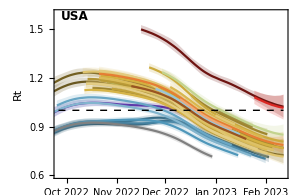
-Graphics- |

```mathematica
fig=Grid[{{countryRtPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt.png

```mathematica
finalRts=Table[If[Length[rtGather["USA",variant]]>0,rtGather["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsLower=Table[If[Length[rtGatherLower["USA",variant]]>0,rtGatherLower["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsUpper=Table[If[Length[rtGatherUpper["USA",variant]]>0,rtGatherUpper["USA",variant][[-1,2]],Null],{variant,variants}];
```

## Prevalence

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I_smooth,I_smooth_upper_95,I_smooth_lower_95,I_smooth_upper_80,I_smooth_lower_80,I_smooth_upper_50,I_smooth_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I_smooth→4,I_smooth_upper_95→5,I_smooth_lower_95→6,I_smooth_upper_80→7,I_smooth_lower_80→8,I_smooth_upper_50→9,I_smooth_lower_50→10,median_freq→11}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{200,100000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,20,100,200,1000,2000,10000,20000,100000,200000,1000000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

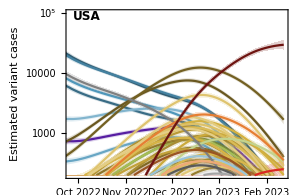
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-log-cases.png

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,32000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

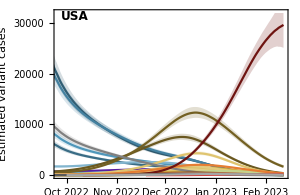
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-cases.png

## Frequency

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
logitTransformDateSeries[dateSeries_]:=Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,dateSeries]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=logitTransformDateSeries[fGather[country,variant]];
lowerSeries=logitTransformDateSeries[fGatherLower[country,variant]];
upperSeries=logitTransformDateSeries[fGatherUpper[country,variant]];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{logitTransform[0.0005],logitTransform[0.9]}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=Show[Table[variantCountryFrequencyPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

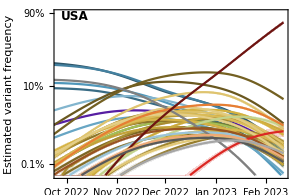
-Graphics- |

```mathematica
fig=Grid[{{countryFrequencyPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-frequency.png

```mathematica
finalFrequencies=Table[fGather["USA",variant][[-1,2]],{variant,variants}];
```

## Rts and frequencies across variants

```mathematica
pos=Flatten[Position[finalRts,x_/;NumberQ[x]]];
```

```mathematica
finalRts=finalRts[[pos]];
```

```mathematica
finalRtsLower=finalRtsLower[[pos]];
```

```mathematica
finalRtsUpper=finalRtsUpper[[pos]];
```

```mathematica
finalFrequencies=finalFrequencies[[pos]];
```

```mathematica
finalVariants=variants[[pos]];
```

```mathematica
finalColors=colors[[pos]];
```

```mathematica
points=ListPlot[Table[{{i,finalRts[[i]]}},{i,Length[finalVariants]}],PlotStyle->finalColors];
```

```mathematica
lines=ListLinePlot[Table[{{i,finalRtsLower[[i]]},{i,finalRtsUpper[[i]]}},{i,Length[finalVariants]}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.35,ImageSize->600,PlotRange->{rtMin,rtMax},FrameTicks->{{Automatic,Automatic},{Table[{i,Rotate[finalVariants[[i]],Pi/2]},{i,Length[finalVariants]}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]}];
```

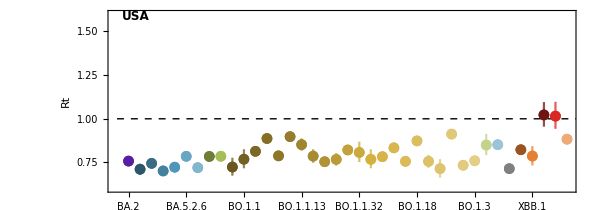

```mathematica
fig=Show[lines,points]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-listplot.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-listplot.png

```mathematica
topPos=Reverse[Ordering[finalRts,-8]];
```

```mathematica
tableValues=Table[{finalVariants[[p]],Round[finalRts[[p]],0.01],ToString[Round[finalRtsLower[[p]],0.01]]<>" - "<>ToString[Round[finalRtsUpper[[p]],0.01]]},{p,topPos}];
```

```mathematica
table=Style[TableForm[tableValues,TableHeadings->{None,{"lineage","Rt estimate","80% uncertainty interval"}},TableSpacing->{3,1}],FontFamily->"Helvetica",FontSize->12];
```

```mathematica
labels=Table[If[MemberQ[topPos,i],finalVariants[[i]],""],{i,Length[finalRts]}];
```

```mathematica
points=ListPlot[MapThread[{{#1,#2}}&,{finalFrequencies,finalRts}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Current lineage frequency","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.65,ImageSize->350,PlotRange->{{0,1},{rtMin,rtMax}},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.2}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]},PlotLabels->Placed[labels,Right]];
```

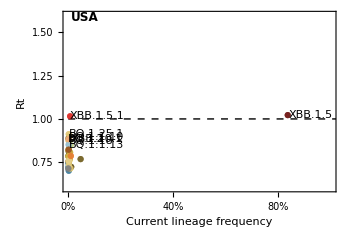
-Graphics- | lineage | Rt estimate | 80% uncertainty interval
XBB.1.5 | 1.02 | 0.95 - 1.1
XBB.1.5.1 | 1.02 | 0.94 - 1.1
BQ.1.25.1 | 0.91 | 0.89 - 0.94
BQ.1.1.10 | 0.9 | 0.87 - 0.92
BQ.1.10.1 | 0.89 | 0.87 - 0.91
XBB.2 | 0.88 | 0.86 - 0.91
BQ.1.18 | 0.87 | 0.85 - 0.89
BQ.1.1.13 | 0.85 | 0.82 - 0.89

```mathematica
fig=Grid[{{points,table}}]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-top.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-top.png